```mathematica
(* Add to path packages *)
packageDirectory=FileNameJoin[{ParentDirectory[ParentDirectory[NotebookDirectory[]]],"1DPackage","*"}];
$Path=Join[$Path,FileNames[packageDirectory]];
```

```mathematica
<<"ReadSintel`"
<<"pyramid1d`"
<<"pyramidalStereoAll`"

methods={"","OverConstrained","SemiConstrained","Constrained","ConstrainedInitialSign","ConstrainedNewMethod","ConstrainedPickierFunction"};
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
```

## Plot: cyclopean-double

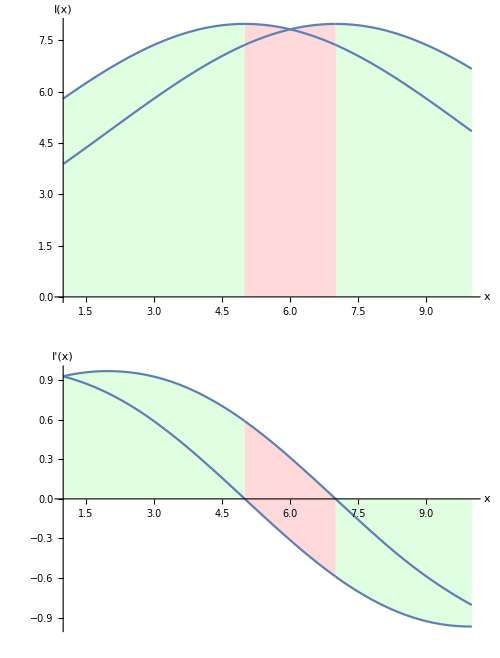

```mathematica
linesize=10;
dis=2;


line1=PDF[NormalDistribution[(linesize)/2,5],Range[1, linesize]]*100//N;
line2=PDF[NormalDistribution[(linesize)/2,5],Range[1-dis, linesize-dis]]*100//N;

{fline1,dfline1}=pyrFuncGen[line1,0][[1]];
{fline2,dfline2}=pyrFuncGen[line2,0][[1]];

ConditionalPlot[func_,condition_,varrange_,xarrange_,yarrange_,trueopts_,falseopts_,lbl_]:=
Module[{plottrue,plotfalse},
plottrue=Plot[If[condition,func],varrange,trueopts,PlotRange->{xarrange,yarrange}];
plotfalse=Plot[If[Not[condition],func],varrange,falseopts,PlotRange->{xarrange,yarrange}];
Show[plottrue,plotfalse,PlotRange->All,AxesLabel->{Style["x",FontSize->fontsize,FontFamily->"Times", Italic],lbl}]
]

fontsize=16;


AA=Block[{x},(
conditional=dfline1[x]*dfline2[x]>0;
ConditionalPlot[{fline1[x],fline2[x]},conditional,{x,1,linesize},{1,linesize},{0,linesize},{Filling->Axis,FillingStyle->LightGreen},{Filling->Axis,FillingStyle->LightRed},Style["I(x)",FontSize->fontsize,FontFamily->"Times", Italic]]
)];

BB=Block[{x},(
conditional=dfline1[x]*dfline2[x]>0;
ConditionalPlot[{dfline1[x],dfline2[x]},conditional,{x,1,linesize},{1,linesize},{-1,linesize},{Filling->Axis,FillingStyle->LightGreen},{Filling->Axis,FillingStyle->LightRed},Style["I'(x)",FontSize->fontsize,FontFamily->"Times", Italic]]
)];

spacings=Scaled[0.08];

g0=Show[
GraphicsColumn[{AA,BB},Spacings->spacings],
Graphics[{Red,Thick,Dashed, Line[{{168,0},{168,-500}}]},AxesOrigin->{0,0}],
Graphics[{Red,Thick,Dashed, Line[{{237,0},{237,-500}}]},AxesOrigin->{0,0}],
ImageSize->500
]
```

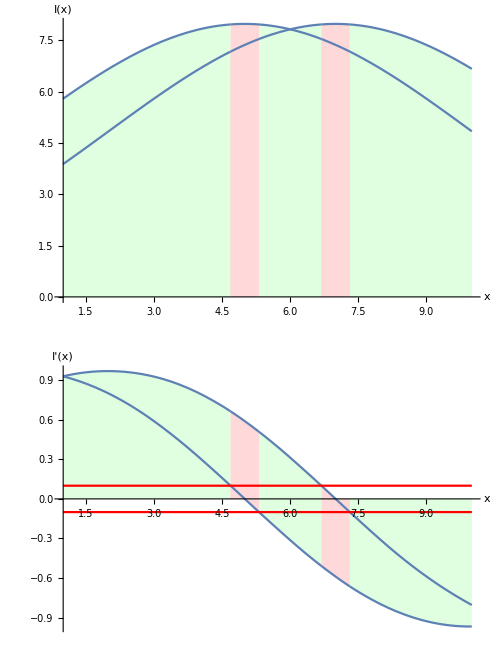

```mathematica
linesize=10;
dis=2;
step=linesize/2;


line1=PDF[NormalDistribution[(linesize)/2,5],Range[1, linesize]]*100//N;
line2=PDF[NormalDistribution[(linesize)/2,5],Range[1-dis, linesize-dis]]*100//N;

{fline1,dfline1}=pyrFuncGen[line1,0][[1]];
{fline2,dfline2}=pyrFuncGen[line2,0][[1]];

ConditionalPlot[func_,condition_,varrange_,xarrange_,yarrange_,trueopts_,falseopts_,lbl_]:=
Module[{plottrue,plotfalse},
plottrue=Plot[If[condition,func],varrange,trueopts,PlotRange->{xarrange,yarrange}];
plotfalse=Plot[If[Not[condition],func],varrange,falseopts,PlotRange->{xarrange,yarrange}];
Show[plottrue,plotfalse,PlotRange->All,AxesLabel->{Style["x",FontSize->fontsize,FontFamily->"Times", Italic],lbl}]
]

fontsize=16;
threshold=0.1;

AA=Block[{x},(
conditional=(Abs[dfline1[x]]>threshold)&&(Abs[dfline2[x]]>threshold);
ConditionalPlot[{fline1[x],fline2[x]},conditional,{x,1,linesize},{1,linesize},{0,linesize},{Filling->Axis,FillingStyle->LightGreen},{Filling->Axis,FillingStyle->LightRed},Style["I(x)",FontSize->fontsize,FontFamily->"Times", Italic]]
)];

BB=Block[{x},(
conditional=(Abs[dfline1[x]]>threshold)&&(Abs[dfline2[x]]>threshold);
ConditionalPlot[{dfline1[x],dfline2[x]},conditional,{x,1,linesize},{1,linesize},{-1,linesize},{Filling->Axis,FillingStyle->LightGreen},{Filling->Axis,FillingStyle->LightRed},Style["I'(x)",FontSize->fontsize,FontFamily->"Times", Italic]]
)];

spacings=Scaled[0.08];

g1=Legended[
Show[
GraphicsColumn[{AA,Show[BB, Plot[{threshold,-threshold},{x, 1, linesize},PlotStyle->Red]]},Spacings->spacings],
Graphics[{Red,Thick,Dashed, Line[{{157,0},{157,-500}}]},AxesOrigin->{0,0}],
Graphics[{Red,Thick,Dashed, Line[{{178,0},{178,-500}}]},AxesOrigin->{0,0}],
Graphics[{Red,Thick,Dashed, Line[{{227,0},{227,-500}}]},AxesOrigin->{0,0}],
Graphics[{Red,Thick,Dashed, Line[{{248,0},{248,-500}}]},AxesOrigin->{0,0}],
ImageSize->500
],
LineLegend[{Red},
{"k"}]]
```

```mathematica
g3=GraphicsRow[{g0,g1}, ImageSize->1300]

figsDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"figs"}];

Export[FileNameJoin[{figsDirectory,"sign-and-mag.pdf"}],g3]
```

-Graphics-

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\sign-and-mag.pdf